```mathematica
Ladder2[n_]:=Block[{i,result={}},
For[i=1,i≤n,i++,
If[i+1≤n,AppendTo[result,i <->i+1],AppendTo[result,i <->2]];
If[i+2≤n,AppendTo[result,i <->i+2],AppendTo[result,i <->1]];
];
Graph[result,VertexLabels->"Name"]
]
```

```mathematica
Table[Ladder2[k]//FindFullFormula//Length,{k,5,10}]
```

{1,8,29,106,491,2449}

```mathematica
Table[Ladder2[k]//FindFullFormula4//Length,{k,5,12}]
```

{0,3,7,7,21,50,77,164}

```mathematica
ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,lambdaKey],x]//NullBaseCoeff
```

{0,-10017714,48565567,-108512513,149684021,-143628713,102117589,-55787628,23900041,-8103096,2174117,-457562,74105,-8930,755,-40,1}

```mathematica
ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,starKey],x]//NullBaseCoeff
```

{0,-17591148,81370368,-172777935,225908561,-205172992,138031633,-71428216,29059294,-9394033,2416320,-490695,77235,-9113,760,-40,1}

```mathematica
Select[GroupBy[Table[{CompleteBaseCoeff[ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,k],x]],allGraphs5[k,"graph"]},{k,allGraphs5AtomKeys}],First->Last],Length[#]>1&]
```

<|{0,0,0,0,10,5000,131141,748574,1508903,1359624,622516,155160,21630,1662,65,1}→{-Graphics-,-Graphics-},{0,0,0,0,6,3551,103568,625157,1308956,1214382,569580,144968,20593,1610,64,1}→{-Graphics-,-Graphics-},{0,0,0,0,14,3255,53148,209548,305588,202783,68229,12225,1165,55,1}→{-Graphics-,-Graphics-},{0,0,0,0,10,2495,42916,176799,267027,182426,62943,11534,1122,54,1}→{-Graphics-,-Graphics-},{0,0,0,0,11,5143,132271,750663,1510322,1360031,622565,155162,21630,1662,65,1}→{-Graphics-,-Graphics-},{0,0,0,0,29,3670,54950,211758,306547,202939,68237,12225,1165,55,1}→{-Graphics-,-Graphics-},{0,0,0,0,8,2361,42259,175838,266416,182246,62920,11533,1122,54,1}→{-Graphics-,-Graphics-},{0,0,0,0,16,3293,53373,209793,305537,202698,68211,12224,1165,55,1}→{-Graphics-,-Graphics-},{0,0,0,0,11,1426,16203,46597,50598,24980,6119,759,45,1}→{-Graphics-,-Graphics-},{0,0,0,0,9,3696,103438,619374,1296107,1204556,566279,144444,20555,1609,64,1}→{-Graphics-,-Graphics-},{0,0,0,0,3,1657,33021,145463,229683,162452,57705,10845,1079,53,1}→{-Graphics-,-Graphics-},{0,0,0,0,8,1947,34494,147410,230594,162613,57714,10845,1079,53,1}→{-Graphics-,-Graphics-},{0,0,0,0,8,2284,41654,173601,263584,180822,62606,11503,1121,54,1}→{-Graphics-,-Graphics-},{0,0,0,0,4,760,10232,32749,38561,20357,5286,691,43,1}→{-Graphics-,-Graphics-},{0,0,0,0,20,3640,55771,214119,308453,203528,68310,12228,1165,55,1}→{-Graphics-,-Graphics-},{0,0,0,0,12,1516,16790,47390,50951,25038,6122,759,45,1}→{-Graphics-,-Graphics-},{0,0,0,0,13,2481,42497,174810,264339,181033,62631,11504,1121,54,1}→{-Graphics-,-Graphics-},{0,0,0,0,5,757,10191,32720,38557,20357,5286,691,43,1}→{-Graphics-,-Graphics-},{0,0,0,0,16,1616,16907,47109,50555,24884,6100,758,45,1}→{-Graphics-,-Graphics-},{0,0,0,0,18,1610,17026,47626,51054,25056,6123,759,45,1}→{-Graphics-,-Graphics-}|>

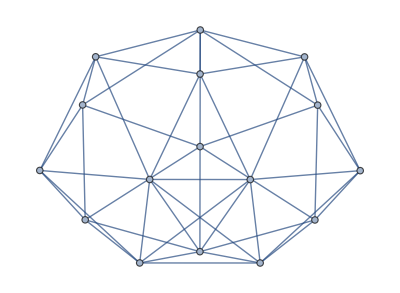
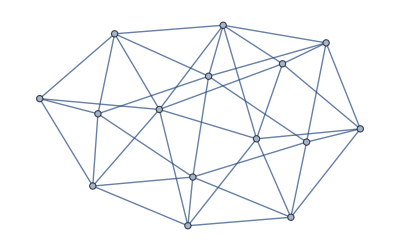
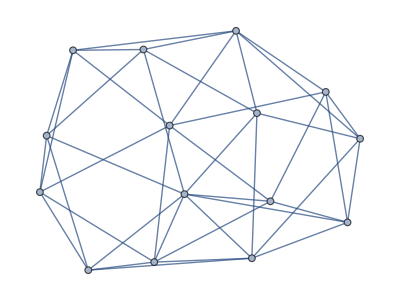
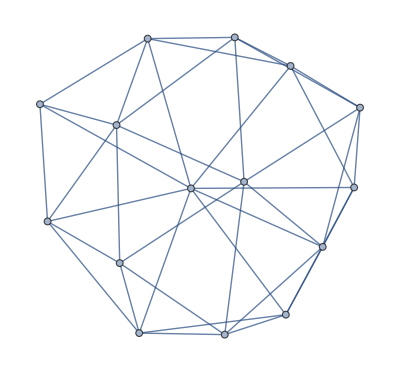
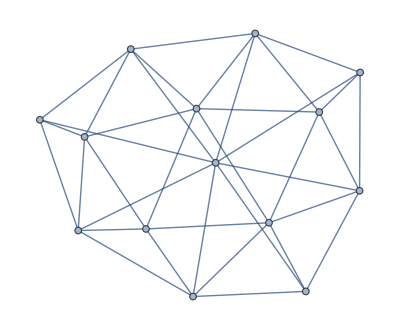
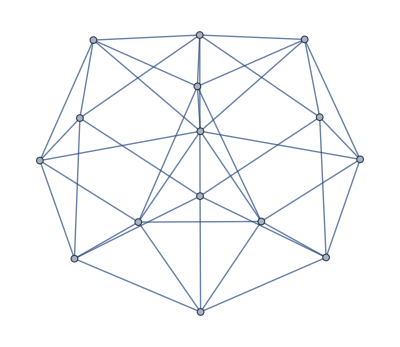
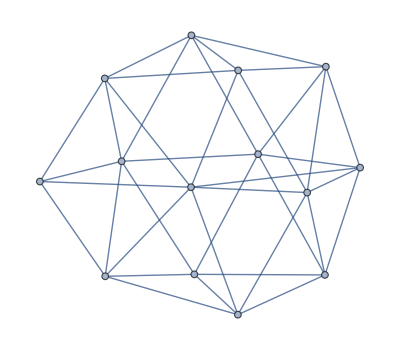
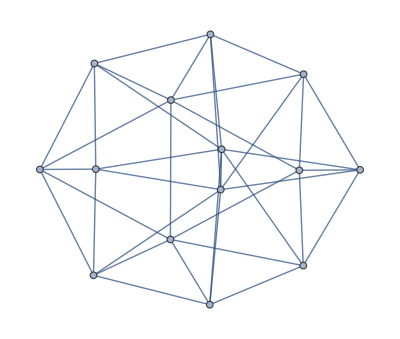
{{{-Graphics-,-Graphics-},1},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},1},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},1},{{-Graphics-,-Graphics-},1},{{-Graphics-,-Graphics-},1},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},1},{{-Graphics-,-Graphics-},1},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},1},{{-Graphics-,-Graphics-},1},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},1},{{-Graphics-,-Graphics-},1},{{-Graphics-,-Graphics-},2},{{-Graphics-,-Graphics-},1}}

```mathematica
Select[Tally[Table[{EmbedGraphInPlantri8[allGraphs5,k],allGraphs5[k,"graph"]},{k,allGraphs5AtomKeys}],IsomorphicGraphQ[#1[[1]],#2[[1]]]&],Length[#]>1&]
```

```mathematica
GraphAutomorphismGroup[plantri8]
```

PermutationGroup[{Cycles[{{1,10},{2,9},{5,11},{6,16},{7,15},{13,17}}],Cycles[{{1,5},{2,13},{3,12},{8,14},{9,17},{10,11}}]}]

```mathematica
IsomorphicGraphQ[EmbedGraphInPlantri8[allGraphs5,k],EmbedGraphInPlantri8[allGraphs5,k]]
```

```mathematica
Select[GroupBy[Table[{CompleteBaseCoeff[ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,k],x]],ShowGraph5Least[k]},{k,allGraphs5GeneratorAtomKeys}],First->Last],Length[#]>1&]
```

<|{0,0,0,0,50,21386,639747,4335120,10512882,11522537,6514613,2051647,374702,40071,2445,78,1}→{-Graphics-295111,-Graphics-291911},{0,0,0,0,10,8942,347643,2743834,7383301,8743524,5253891,1739261,331313,36744,2315,76,1}→{-Graphics-295230,-Graphics-292810},{0,0,0,0,6,7493,320070,2620417,7183354,8598282,5200955,1729069,330276,36692,2314,76,1}→{-Graphics-295210,-Graphics-294430},{0,0,0,0,37,19124,602404,4180208,10274742,11356591,6456218,2040740,373621,40018,2444,78,1}→{-Graphics-294151,-Graphics-292511},{0,0,0,0,11,9085,348773,2745923,7384720,8743931,5253940,1739263,331313,36744,2315,76,1}→{-Graphics-287950,-Graphics-98410},{0,0,0,0,60,18393,539111,3714262,9206304,10308718,5945090,1906681,354109,38461,2381,77,1}→{-Graphics-287861,-Graphics-98321},{0,0,0,0,25,14997,494600,3546918,8960092,10140559,5886440,1895764,353028,38408,2380,77,1}→{-Graphics-287141,-Graphics-98381},{0,0,0,0,37,17378,533287,3704290,9199160,10306253,5944667,1906647,354108,38461,2381,77,1}→{-Graphics-285521,-Graphics-98401},{0,0,0,0,125,37279,938803,5729769,12952302,13495431,7342665,2243550,399829,41898,2513,79,1}→{-Graphics-284625,-Graphics-98285},{0,0,0,0,9,7638,319940,2614634,7170505,8588456,5197654,1728545,330238,36691,2314,76,1}→{-Graphics-273370,-Graphics-229630},{0,0,0,0,18,12846,456529,3385254,8709144,9965290,5824939,1884358,351910,38354,2379,77,1}→{-Graphics-273340,-Graphics-228820},{0,0,0,0,28,13721,462711,3396462,8716557,9967328,5825172,1884367,351910,38354,2379,77,1}→{-Graphics-273100,-Graphics-229360},{0,0,0,0,27,14922,492735,3536809,8942992,10128902,5882776,1895208,352989,38407,2380,77,1}→{-Graphics-270941,-Graphics-229621},{0,0,0,0,69,29468,825243,5298805,12333271,13087391,7205808,2219068,397498,41788,2511,79,1}→{-Graphics-270643,-Graphics-228543},{0,0,0,0,50,21421,639123,4327990,10498183,11511639,6511045,2051095,374663,40070,2445,78,1}→{-Graphics-266071,-Graphics-30371},{0,0,0,0,110,36689,934961,5716568,12932453,13482480,7338709,2242965,399789,41897,2513,79,1}→{-Graphics-263645,-Graphics-30365},{0,0,0,0,39,18813,598276,4165264,10254122,11343902,6452430,2040179,373582,40017,2444,78,1}→{-Graphics-222311,-Graphics-75731},{0,0,0,0,61,28725,820403,5291334,12329701,13087048,7205918,2219090,397499,41788,2511,79,1}→{-Graphics-221503,-Graphics-75703},{0,0,0,0,175,51661,1265571,7464048,16300188,16426975,8657644,2566234,444258,45277,2644,81,1}→{-Graphics-200348,-Graphics-7608},{0,0,0,0,172,51946,1269900,7480935,16323626,16441106,8661748,2566825,444298,45278,2644,81,1}→{-Graphics-68168,-Graphics-22788}|>

```mathematica
Table[ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,k],x],{k,allGraphs5GeneratorAtomKeys}]//DeleteDuplicates//Length
```

32

```mathematica
Table[ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,k],x],{k,allGraphs5NullAtomKeys}]//DeleteDuplicates//Length
```

32

```mathematica
Table[ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,k],x],{k,allGraphs5AtomKeys}]//DeleteDuplicates//Length
```

32

```mathematica
Table[ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,k],x],{k,allGraphs5FakeAtomKeys}]//DeleteDuplicates//Length
```

32

```mathematica
VertexCount[Graph[plantri[[10000]]]]
```

24

```mathematica
Monitor[Table[ChromaticPolynomial[EmbedGraph5[allGraphs5,k],x],{k,allGraphs5NullAtomKeys}]//DeleteDuplicates//Length,ShowGraph5Least[k]]
```

48